Classifier for Spatial Orientations of a 3D Object

Jan Segert

Guilio Alessandrini

University of Missouri

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: To train a neural network to identify spatial rotations from images of a 3D object.

SUMMARY OF WORK:  The initial step was to train a simple classifier to detect planar (2D) rotations of a planar object (triangle).   The main part of work was training a classifier to detect non-planar rotations of an imaged 3D object (Ironman helmet).   Most of the work focused on the special case of nonplanar rotations about the vertical axis in the image plane.

RESULTS AND FUTURE  WORK: Identifying planar rotations of a triangle is as easy as pie.  Nonplanar rotations about a fixed axis can be identified reasonably well, with a little thought about fine-tuning networks.   Identifying arbitrary nonplanar rotations will require future work, but in principle should work as well as the case of fixed rotation axis.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

#### Training a network involves many choices, and the opportunity to learn from past mistakes. Criteria for a successfully trained network are:

The points in the left picture should lie on the unit circle.

The line segments in the right picture should be close to radial (denoted by red color).

Network 1: The point cloud is close to the unit circle only in the first quadrant, and it is diffuse.  The lines are mostly radial only in the first quadrant, and chaotic.  (not (HelmetsTrain6.nb, “level5round1.wlnet”)

Network 1a is a fine-tuning of network 1, transferring the previous learning and training more layers.    The point cloud is less diffuse (good), but the overall fit to the circle is not better (bad).   The line segments are only radial in the second quadrant, but less chaotic.  (HelmetsTrain6.nb,“level5round2.wlnet”)

Network 2 is designed to constrain the point to the unit circle (think Lagrange multipliers).   The points are not close to the unit circle, but they are close to a smaller circle.  The line segments are chaotic, but the pattern is uniform. (from HelmetsTrain8, "constrainedMacNet.wlnet")

Network 2a is a fine-tuning of Network 1 using transfer of learning from network 1.  The modification is  sharper constraint enforcement.  This is something of an improvement, but not uniform across the circle.  (from HelmetsTrain8, “tunedSharpNet.wlnet”)

Network 2b is a fine-tuning of Network 2a, transferring learning and training more layers.  This is an improvement.  The points are uniformly close to the circle, and the line segments are largely radial and nonchaotic.   But there are regions where there is a systematic error (denoted by green).  (from HelmetsTrain8, “tunedSharpNet.wlnet”)

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

The main result was the largely successful incremental training of  large convolutional network to identify nonplanar rotations of single three-dimensional object. For simplicity of diagnosing and tuning the results, the rotations were limited to rotations about the vertical axis in the image plane.  This case is simpler since the restricted rotation group SO(2) can be described as a circle in two-dimensions, which is easily visualized.   The full rotation group is higher-dimensional, making analogous visualizations of results more difficult.    The results obtained for the restricted rotation group SO(2) should generalize to allow for arbitrary three-dimensional rotations in SO(3) of a single object.  

The key feature was the introduction of  a network layer to dynamically enforce the constraint that a sequence of numbers satisfy a (nonlinear) constraint.    This made it possible to incrementally transfer learning and tune the network with good results.   In contrast, network architectures that did not enforce this constraint on the output gave results that did not satisfy the constraint, and were therefore a poor fit.

Code

Provide one of:

Link to the GitHub

Explicit code

#### Generation of initial training/validation/test data (Helmets6.nb). Objecdt is rotated about the vertical axis in the image plane, and illuminated by with three random colors each from a separate random direction in the front hemisphere. It takes about a second to generate one element of the training set, so only a few thousand elements can be generated within the time constraints. The image is generated along with the {Cos,Sin} of the rotation angle.

Mesh of 3D object (.stl format, downloaded from thingiverse.com)

```mathematica
iron =-Graphics3D-;
```

```mathematica
helmetType=iron;
```

random unit vector

```mathematica
randomUnitVector := RandomVariate[CircularRealMatrixDistribution[3]].{1,0,0}
```

random vector in front hemisphere, used for lighting directions to avoid lighting from the back

```mathematica
frontVec[refVec_] := Module[{tempVec =randomUnitVector},If[tempVec.refVec ≥ 0,tempVec,-tempVec]]
```

Generating a training set

```mathematica
helmetName = "iron"
helmetType = ToExpression[helmetName];
setIndex = 0
sampsize =5
imsize=64;

ClearAll[temp]
temp =Table[ranAng=RandomReal[2 Pi];
cs=Cos[ranAng];
ss=Sin[ranAng];
color1=Hue[RandomReal[1]];
color2=Hue[RandomReal[1]];
color3=Hue[RandomReal[1]];
rotMat={{cs,ss,0},{-ss,cs,0},{0,0,1}};
 viewVec=rotMat.{0,-1.5,0};
s=Show[helmetType,ViewPoint->viewVec,Lighting->{
{"Directional",color1,{frontVec[viewVec],{0,0,0}}},{"Directional",color2,{frontVec[viewVec],{0,0,0}}},{"Directional",color3,{frontVec[viewVec],{0,0,0}}}
},ImageSize->imsize];
im=Rasterize[s,"Image",ImageSize-> {imsize,imsize}];
im -> {cs,ss}
,{nls,1,sampsize}]

Export[StringJoin[helmetName,"Helm",ToString[setIndex],".m"],temp]
```

iron

0

5

{-Graphics-→{-0.874169,-0.485622},-Graphics-→{0.946829,-0.321738},-Graphics-→{-0.817124,0.576462},-Graphics-→{0.204362,0.978895},-Graphics-→{-0.351029,-0.936365}}

ironHelm0.m

#### Data augmentation generates more training set elements from the initial training set, more quickly than generating new images. This allows generation of a large training set ( 152960 elements), validation set ( 38240 element), and test set (about 1000 elements) within time constraints.

Data Augmentation by reflection (angle must also be flipped)

{-Graphics-→{-0.443424,0.896312},-Graphics-→{-0.0167844,0.999859},-Graphics-→{0.138548,0.990356},-Graphics-→{-0.809705,0.586837},-Graphics-→{0.980476,0.196638}}

```mathematica
keysReflect[image_] := ImageReflect[image,Left-> Right]
```

```mathematica
valuesReflect[twovec_] := {First[twovec],-Last[twovec]}
```

```mathematica
ClearAll[reflectRule]
reflectRule[rule_] := keysReflect[Keys[rule]]-> valuesReflect[Values[rule]]
SetAttributes[reflectRule,Listable]
```

```mathematica
reflectRule[temp]
```

{-Graphics-→{-0.874169,0.485622},-Graphics-→{0.946829,0.321738},-Graphics-→{-0.817124,-0.576462},-Graphics-→{0.204362,-0.978895},-Graphics-→{-0.351029,0.936365}}

Data Augmentation by shifts (small shifts such as 1 or 2 pixels are used, a large shift is used below for demonstration purposes)

```mathematica
ClearAll[verticalShift]
verticalShift[image_,range_] := Module[{temp,shift=RandomInteger[{1,Abs[range]}],sign=1-2*RandomInteger[1]},
temp=ImageTake[image,Sign[sign]*(64-shift)];
ImagePad[temp,{{0,0},{(1/2)*(-sign+1)shift,(1/2)*(sign+1)shift}},White]
]
```

```mathematica
clockwise[image_] :=ImageRotate[image,Top->Right]
counterclockwise[image_] :=ImageRotate[image,Top->Left]
```

```mathematica
ClearAll[horizontalShift]
horizontalShift[image_,range_] :=counterclockwise[ verticalShift[clockwise[image],range]]
```

```mathematica
ClearAll[fullShift]
fullShift[image_,range_] := verticalShift[horizontalShift[image,range],range]
```

```mathematica
ClearAll[shiftRule]
shiftRule[rule_,range_]:= fullShift[Keys[rule],range]-> Values[rule]
SetAttributes[shiftRule,Listable]
```

```mathematica
shiftRule[temp,30]
```

{-Graphics-→{-0.874169,-0.485622},-Graphics-→{0.946829,-0.321738},-Graphics-→{-0.817124,0.576462},-Graphics-→{0.204362,0.978895},-Graphics-→{-0.351029,-0.936365}}

Data Augmentation by color jittering

```mathematica
ClearAll[jitterColor]
jitterColor[image_] := Module[{hsbsep=ColorSeparate[ColorConvert[image,"HSB"]]},
hsbsep[[1]]=ImageMultiply[hsbsep[[1]],RandomReal[{0.7,1.4}]];
hsbsep[[1]]=ImageAdd[hsbsep[[1]],RandomReal[{-0.1,0.1}]];
hsbsep[[2]]=ImageMultiply[hsbsep[[1]],RandomReal[{0.7,1.4}]];
hsbsep[[2]]=ImageAdd[hsbsep[[1]],RandomReal[{-0.1,0.1}]];
ColorConvert[ColorCombine[hsbsep,"HSB"],"RGB"]
]
SetAttributes[jitterColor,Listable]
```

```mathematica
ClearAll[jitterColorRule]
jitterColorRule[rule_] := jitterColor[Keys[rule]]-> Values[rule]
SetAttributes[jitterColorRule,Listable]
```

```mathematica
jitterColorRule[temp]
```

{-Graphics-→{-0.874169,-0.485622},-Graphics-→{0.946829,-0.321738},-Graphics-→{-0.817124,0.576462},-Graphics-→{0.204362,0.978895},-Graphics-→{-0.351029,-0.936365}}

#### Network 1 starts with a large convolultion network trained to classify natural images, and modifies the final layer from a discrete classification to a measurment of two numbers (Cos and Sin of the rotation angle)

```mathematica
NetReplacePart[Drop[NetModel["SqueezeNet V1.1 Trained on ImageNet Competition Data"],-2],"Input"->NetEncoder[{"Image",{64,64},"ColorSpace"->"RGB"}]]
```

NetChain[]

```mathematica
Normal@Drop[NetModel["SqueezeNet V1.1 Trained on ImageNet Competition Data"],-2]
```

<|conv1→ConvolutionLayer[<>],relu_conv1→ElementwiseLayer[<>],pool1→PoolingLayer[<>],fire2→NetGraph[],fire3→NetGraph[],pool3_pad→PaddingLayer[<>],pool3→PoolingLayer[<>],fire4→NetGraph[],fire5→NetGraph[],pool5_pad→PaddingLayer[<>],pool5→PoolingLayer[<>],fire6→NetGraph[],fire7→NetGraph[],fire8→NetGraph[],fire9→NetGraph[],drop9→DropoutLayer[<>],conv10→ConvolutionLayer[<>],relu_conv10→ElementwiseLayer[<>],pool10→AggregationLayer[<>]|>

```mathematica
net=NetChain[Append[
Normal[
NetReplacePart[Drop[NetModel["SqueezeNet V1.1 Trained on ImageNet Competition Data"],-2],"Input"->{3,64,64}]
],
"classifier"->LinearLayer[2]
],
"Input"->NetEncoder[{"Image",{64,64},"ColorSpace"->"RGB"}]
]
```

NetChain[]

The LearningRateMultipliers are set as below to train the last three layers while freezing all of the other layers (nonexecutable code given here since the data is not available)

trainedNet = NetTrain[
	net, 
	trainingSet, 
	ValidationSet → validationSet, 
	LearningRateMultipliers → {
		"classifier" -> 1, 
		"conv10" -> 1, 
		"fire9" -> 1, 
		_ -> None}
]

#### Network 1a is fine-tuning of network 1.

The LearningRateMultipliers are set to unfreeze the initial layers, but to train them with lower weight:

fineTunedNet = NetTrain[
	trainedNet, 
	trainingSet, 
	ValidationSet -> validationSet, 
	LearningRateMultipliers -> {
		"classifier" -> 1, 
		"conv10" -> 1, 
		"fire9" -> 1, 
		_ -> 0.3
	}
]

#### Network 2 implements a constraint before the last layer, to dynamically enforce the constraint x^2 +y^1 = 1 on the two components {x,y} = {Cos,Sin}.

The training/validation/test sets are modified by changing {x,y} to {x,y,0}, as illustrated by

```mathematica
rsmod={-Graphics-->{0.9047630485611374,0.42591528025929865,0},-Graphics-->{0.9979251503659802,-0.06438473628924689,0}};
```

```mathematica
ClearAll[net,ynet]
```

```mathematica
ynet=NetGraph[Association[
"part1"->PartLayer[1],
"part2"->PartLayer[2],
"constraint"->ThreadingLayer[#1^2+#2^2-1&],
"reshape"->ReshapeLayer[{1}],
"catenate"->CatenateLayer[]
],
{
"part1"->"constraint",
"part2"->"constraint",
NetPort["Input"]->"catenate",
"constraint"->"reshape"->"catenate"
},
"Input"->2 (* this means the input is 2-component vector *)
]
```

NetGraph[]

```mathematica
net=NetChain[Join[
Normal[
NetReplacePart[Drop[NetModel["SqueezeNet V1.1 Trained on ImageNet Competition Data"],-2],"Input"->{3,64,64}]
],
Association[
"classifier"->LinearLayer[2],
"output"->ynet
]
],
"Input"->NetEncoder[{"Image",{64,64},"ColorSpace"->"RGB"}]
]
```

NetChain[]

The network is trained with large learning multipliers on the last 3 layers, and small ones on the initial layers (almost freezing these already trained layers)

trainedNet = NetTrain[
	net ,trainingSet,
	ValidationSet→validationSet,
	LearningRateMultipliers → {
			"classifier" → 1,
			"conv10"     → 0.5,
			"fire9"      → 0.5,
			"fire8"      → 0.5,
			"fire7"      → 0.5,
			_            → 0.1
		},
	MaxTrainingRounds → 9
]

#### Network 2a sharpens the constraint, by placing a larger multiplier of 4 instead of 1 on the constraint function

```mathematica
ynetSharp=NetGraph[Association[
"part1"->PartLayer[1],
"part2"->PartLayer[2],
"constraint"->ThreadingLayer[4Abs[(#1^2+#2^2-1)]&], (* Multiply constrait by 4 of absolute value  *)
"reshape"->ReshapeLayer[{1}],
"catenate"->CatenateLayer[]
],
{
"part1"->"constraint",
"part2"->"constraint",
NetPort["Input"]->"catenate",
"constraint"->"reshape"->"catenate"
},
"Input"->2 (* this means the input is 2-component vector *)
]
```

NetGraph[]

This is appended to the previously trained network 2: 

sharpNet =Import[“constrainedMacNet.wlnet”]

NetChain[Append[Normal[sharpNet],”output”→ ynetSharp],
“Input”→NetEncoder[{“Image”,{64,64},”ColorSpace”→”RGB”}]]

The learning multipliers are set to train the last three layers, and freeze the remaining layers. The number of training rounds is small, but results in a significant change.

tunedSharpNet = NetTrain[
	sharpNet, 
	trainingSet, 
	ValidationSet -> validationSet, 
	LearningRateMultipliers -> {
		"classifier" -> 1, 
		"conv10" -> 1, 
		"fire9" -> 1, 
		"fire8" -> None, 
		"fire7" -> None, 
		_ -> None
	}, 
MaxTrainingRounds -> 3
]

#### Network 2b fine-tunes the trained network 2a.

The learning multipliers are set to train all layers, but with larger weights on the last layers, small rates on the initial layers, and intermediate weights on the intervening layers.

tunedSharpNet2alt = NetTrain[
	tunedSharpNet, 
	trainingSet, 
	ValidationSet -> validationSet, 
	LearningRateMultipliers -> {
		"classifier" -> 0.5, 
		"conv10" -> 0.5, 
		"fire9" -> 0.5, 
		"fire8" -> 0.2, 
		"fire7" -> 0.2, 
		_ -> None}, 
	MaxTrainingRounds -> 10
]

Written Content / Lesson Plans

Conclusions in Detail

It is known that previously trained large convolutional networks can be used as the starting point for new image identifications tasks, using transfer learning and fine-tuning.   In this project we modified a previously trained image classification network to a regression network, retaining the trained initial stages.    The goal was to measure rotations of a 3D object from images, focusing on the special case of rotations about the vertical axis in the image plane.  
 This had some success, but there were complications in that the regression output satisfied a nonlinear constraint which was not enforced by the network, and resulted in more and more drift of the results during subsequent transfer learning and fine-tuning stages.  

The main technique introduced here is the addition of a network layer to dynamically enforce the nonlinear constraint on the output.   Using several stages of transfer learning and fine tuning, this resulted in good results.   We focused on one nonlinear constraint on two-dimensional output data.   The same techniques should generalize to more nonlinear constraints on higher-dimensional output data, for example for the matrices describing the entire group of rotations in 3D space.

All Visualizations

The generation of the main visualization was made as follows.   The data corresponding to the correct rotation of a test image is in the list “vin”, the rotation of the same image as measured by the network (network 2b in this case) is in the file “vout”.

```mathematica
vin
```

{{-0.285704,-0.958318},{-0.936436,-0.350838},{0.56413,-0.825686},{0.113999,0.993481},{0.98709,0.160165},{0.942909,0.33305},{0.654866,-0.755745},{-0.994749,-0.102347},{-0.942631,-0.333837},{-0.128255,-0.991741},{-0.974673,0.223633},{0.658546,0.752541},{0.183046,-0.983104},{-0.83072,-0.556691},{0.0968539,-0.995299},{0.737208,0.675666},{0.132332,0.991205},{-0.113037,0.993591},{0.944089,0.329692},{0.744434,-0.667697},{-0.458064,0.888919},{0.480676,0.876898},{0.790594,-0.61234},{0.921431,-0.388541},{0.979188,0.202954},{0.899445,0.437034},{-0.434376,-0.900732},{-0.513131,0.858311},{-0.977338,0.211686},{0.967437,-0.253111},{-0.998094,0.0617105},{-0.581549,-0.813511},{0.027998,-0.999608},{-0.938482,-0.345329},{0.206294,-0.97849},{-0.640599,0.767876},{0.0053184,-0.999986},{-0.629181,-0.777258},{-0.247649,0.96885},{0.882381,0.470536},{0.967735,-0.251969},{-0.0424098,0.9991},{-0.172576,0.984996},{0.909313,0.416112},{-0.694091,0.719887},{-0.419049,-0.907964},{-0.868281,-0.496073},{0.954639,-0.297764},{-0.969065,0.246805},{0.995591,0.0937987},{0.725112,-0.688631},{0.471926,0.881638},{0.211985,0.977273},{0.967193,-0.254042},{-0.994968,0.100194},{0.025677,-0.99967},{-0.909933,0.414755},{-0.502072,-0.864826},{-0.194423,0.980918},{0.577053,-0.816707},{-0.140547,-0.990074},{0.848744,0.528805},{-0.962997,-0.269511},{0.951413,0.307917},{-0.656809,0.754057},{0.343972,0.93898},{-0.982352,0.187041},{0.0257002,0.99967},{0.692549,-0.721371},{-0.998263,-0.0589076},{0.91641,-0.400242},{0.327488,-0.944855},{0.109896,0.993943},{-0.777213,-0.629237},{-0.500494,0.86574},{-0.912861,-0.408271},{-0.163927,0.986473},{-0.29718,0.954822},{0.365166,0.930942},{-0.911826,-0.410578},{0.0138695,-0.999904},{-0.996681,-0.0814005},{0.659778,0.751461},{-0.00828988,-0.999966},{-0.563859,0.825871},{0.68278,0.730624},{0.721948,-0.691947},{0.763887,0.64535},{-0.276445,0.96103},{-0.786988,0.616968},{0.987782,-0.155844},{0.938768,0.344551},{0.272862,-0.962053},{0.993676,0.112289},{-0.964964,0.262383},{0.956529,-0.291636},{-0.726084,0.687607},{-0.917524,-0.397681},{-0.958362,0.285556},{-0.0105195,0.999945},{-0.674915,0.737896},{-0.560976,0.827832},{-0.100295,0.994958},{-0.813908,0.580994},{-0.342161,0.939641},{0.709232,0.704975},{-0.339829,0.940487},{0.991723,-0.128394},{0.447091,0.894489},{0.917969,0.396653},{-0.919026,0.394197},{0.473491,0.880799},{-0.988554,-0.150869},{-0.971956,0.235164},{-0.0486134,-0.998818},{-0.0682096,-0.997671},{0.943496,-0.331385},{0.0811792,0.9967},{-0.533809,0.845605},{-0.92419,-0.381934},{0.72363,-0.690189},{-0.939719,-0.341949},{0.388632,0.921393},{-0.476168,-0.879354},{-0.112067,0.993701},{-0.848094,-0.529846},{-0.876598,0.481223},{0.261212,-0.965281},{0.940643,0.339396},{-0.446345,-0.894861},{0.204827,-0.978798},{-0.66972,-0.742614},{0.0890025,-0.996031},{0.71127,0.702919},{0.753449,-0.657506},{0.111122,-0.993807},{0.728128,-0.685441},{-0.907364,0.420345},{0.727938,0.685643},{0.534756,-0.845007},{-0.327402,0.944885},{-0.0674697,0.997721},{0.727973,0.685605},{0.466573,-0.884483},{0.266054,-0.963958},{-0.0519163,0.998651},{-0.507381,0.861722},{-0.65625,0.754544},{0.328212,-0.944604},{0.994566,-0.104113},{0.97487,-0.222776},{-0.991076,0.133295},{-0.842377,0.538888},{-0.0135877,-0.999908},{-0.00677284,0.999977},{0.0201161,0.999798},{-0.998693,0.0511064},{-0.921029,-0.389494},{-0.857491,0.514498},{0.22299,0.974821},{0.980732,0.195356},{-0.0508489,-0.998706},{0.999498,-0.0316755},{-0.99491,-0.100763},{0.593068,0.805152},{-0.276629,0.960977},{0.919602,-0.392851},{0.870612,0.49197},{0.118851,-0.992912},{0.443768,0.896142},{0.990692,0.136122},{0.321082,0.947051},{-0.692539,-0.72138},{-0.335542,0.942025},{0.937483,0.348032},{-0.654218,0.756306},{-0.549877,-0.835246},{0.377253,-0.92611},{-0.371487,-0.928438},{0.715832,-0.698273},{0.266054,-0.963958},{-0.845357,-0.534202},{-0.986664,0.162769},{0.98452,-0.175274},{-0.766561,-0.642171},{-0.0816429,-0.996662},{-0.966701,-0.255909},{-0.683216,0.730216},{0.64384,0.76516},{-0.0470824,0.998891},{0.435123,-0.900371},{-0.879836,0.475277},{-0.996716,0.0809765},{-0.411147,0.911569},{-0.853338,0.521358},{0.160788,-0.986989},{-0.975941,-0.218035},{0.754295,-0.656536},{-0.365986,-0.93062},{0.765448,0.643497},{-0.597423,0.801926},{0.992553,-0.121811},{0.235209,0.971945},{-0.943115,-0.332467},{0.941324,-0.337504},{0.954423,0.298456},{-0.865369,-0.501135},{0.156439,-0.987688},{0.0116993,0.999932},{0.281515,-0.959557},{-0.814703,-0.579878},{-0.907754,-0.419502},{0.571014,0.82094},{0.956529,0.291636},{0.921228,0.389024},{0.967772,-0.251826},{0.996053,-0.0887581},{0.532566,0.846388},{0.0246203,-0.999697},{0.980215,-0.197938},{-0.434181,0.900826},{0.671117,0.741351},{0.820216,-0.572054},{0.362392,-0.932026},{-0.925755,0.378124},{0.0900512,0.995937},{0.143799,-0.989607},{-0.627669,0.778481},{0.996292,-0.0860413},{0.289474,0.957186},{-0.0712765,0.997457},{0.975415,0.220376},{-0.0769256,-0.997037},{-0.982156,0.188066},{0.54845,0.836183},{-0.285268,0.958448},{0.285059,0.95851},{-0.234843,-0.972033},{0.770899,0.636958},{0.938694,-0.344753},{0.765318,-0.643652},{0.863237,-0.504799},{0.809107,0.587661},{0.624172,-0.781287},{0.963921,-0.266187},{-0.340108,-0.940386},{-0.114063,-0.993473},{-0.14769,0.989034},{0.947549,0.319612},{0.559971,-0.828512},{-0.997304,-0.0733815},{0.839523,-0.543324},{0.562858,-0.826554},{-0.212623,0.977134},{-0.759353,-0.650679},{0.548835,0.83593},{-0.74315,-0.669125},{0.728855,0.684668},{-0.963908,0.266237},{0.0532589,-0.998581},{-0.595046,-0.803692},{0.38277,-0.923844},{-0.680056,0.73316},{0.301632,-0.953425},{0.998442,0.0557945},{0.965517,0.260338},{-0.949655,-0.313299},{-0.383827,0.923405},{0.33755,-0.941308},{-0.0996195,-0.995026},{-0.741639,0.670799},{-0.287818,0.957685},{0.994995,0.0999262},{-0.192727,-0.981252},{-0.432864,-0.901459},{0.96028,-0.279039},{-0.664533,-0.747259},{-0.855732,-0.51742},{-0.936876,-0.349662},{-0.970556,0.240874},{-0.381656,-0.924305},{-0.629156,0.777279},{-0.698984,-0.715137},{-0.371943,0.928256},{0.947862,-0.318681},{0.776949,-0.629563},{-0.925664,0.378346},{0.495392,0.86867},{-0.554891,0.831923},{0.984117,0.17752},{0.98834,-0.152264},{-0.972542,-0.232729},{0.340476,0.940253},{0.221282,0.97521},{-0.833899,-0.551917},{0.148539,-0.988907},{0.0484386,0.998826},{-0.821086,0.570805},{0.108421,0.994105},{0.975165,0.22148},{0.984062,-0.177828},{0.304525,-0.952504},{-0.568998,0.822339},{0.00123976,0.999999},{-0.148055,0.988979},{0.8971,0.441827},{-0.985395,-0.170282},{-0.9866,0.16316},{0.912428,0.409238},{0.163276,0.986581},{-0.985606,-0.169059},{-0.19992,-0.979812},{0.695097,0.718916},{0.987411,-0.158175},{0.438763,0.898603},{0.867024,-0.498267},{-0.973983,-0.22662},{-0.657762,-0.753226},{-0.476083,-0.8794},{0.998237,-0.0593524},{0.902503,0.430684},{0.784617,0.619981},{0.62455,-0.780985},{0.121803,0.992554},{-0.809891,0.586581},{-0.232769,-0.972532},{-0.988214,0.153079},{-0.556415,-0.830905},{-0.971943,0.235215},{-0.985469,0.169855},{-0.403204,0.91511},{-0.451259,-0.892393},{0.269988,-0.962864},{0.652683,0.757631},{-0.981965,0.189062},{-0.834924,0.550365},{-0.97071,-0.240256},{-0.837137,0.546994},{0.77957,-0.626316},{-0.779396,-0.626531},{0.486655,0.873594},{-0.506453,0.862267},{0.906189,-0.422872},{-0.771996,-0.635627},{0.666279,0.745703},{0.0467466,0.998907},{0.125778,-0.992058},{0.989794,0.142508},{0.0265204,-0.999648},{0.615158,0.788404},{-0.608054,0.793895},{0.999775,-0.0212119},{-0.829533,0.558458},{-0.994783,0.102014},{0.740033,-0.672571},{-0.999951,0.00984902},{-0.924793,0.38047},{-0.422404,-0.906408},{-0.782174,0.623061},{0.965531,0.260289},{0.95024,-0.311519},{0.71963,-0.694358},{-0.238243,0.971206},{0.388632,0.921393},{0.995019,0.0996876},{-0.628523,0.777791},{-0.12319,0.992383},{0.715087,0.699035},{-0.630802,-0.775944},{0.975617,-0.21948},{-0.884542,-0.466461},{-0.999951,0.00984902},{0.898218,0.439551},{0.961382,-0.275217},{0.982501,0.186257},{0.329289,-0.944229},{-0.52843,-0.848977},{-0.18422,-0.982885},{0.0954141,0.995438},{0.254002,0.967204},{0.745139,0.666909},{0.357049,0.934086},{-0.284103,0.958794},{0.816271,-0.57767},{0.383052,0.923727},{0.594902,-0.803798},{0.913218,0.407472},{-0.78013,0.625618},{-0.928073,0.372398},{0.542074,-0.840331},{0.775196,0.631721},{0.126402,0.991979},{-0.663116,-0.748516},{-0.752129,-0.659016},{0.391848,0.92003},{-0.784873,-0.619657},{-0.690401,-0.723426},{0.988601,0.150558},{0.52285,-0.852425},{0.0714398,0.997445},{-0.902853,-0.429949},{0.954342,-0.298715},{-0.999736,0.0229681},{-0.843081,-0.537786},{0.836159,-0.548488},{0.0248763,0.999691},{-0.25693,0.96643},{-0.894609,0.44685},{0.42349,-0.905901},{-0.534063,-0.845445},{-0.917498,0.397741},{0.318697,0.947857},{-0.569556,-0.821952},{0.826609,-0.562777},{-0.869611,-0.493737},{0.508635,0.860982},{-0.199427,-0.979913},{-0.976764,0.214318},{0.280361,-0.959895},{0.253671,-0.967291},{0.0358046,-0.999359},{0.956066,-0.293152},{0.492216,-0.870473},{-0.999116,-0.0420473},{0.857195,0.514992},{-0.280925,0.95973},{0.747247,0.664546},{-0.480055,-0.877238},{0.298237,0.954492},{0.919772,0.392454},{-0.604122,-0.796892},{-0.999952,0.00979236},{0.141839,-0.98989},{0.365713,0.930727},{0.769426,-0.638736},{0.228852,0.973461},{-0.688718,-0.725029},{-0.81615,-0.57784},{0.979209,0.202852},{0.800729,-0.599027},{-0.200974,0.979596},{0.263196,0.964742},{0.557862,0.829933},{0.801625,0.597828},{-0.842781,0.538257},{-0.511554,-0.859251},{0.980914,-0.194441},{0.474007,-0.880521},{0.591439,-0.80635},{0.200299,-0.979735},{0.001037,0.999999},{-0.929257,-0.369434},{0.264437,-0.964403},{-0.974464,0.224546},{-0.550711,0.834696},{0.802705,-0.596376},{-0.357116,0.93406},{0.111116,-0.993807},{-0.993348,-0.115154},{-0.890412,0.455156},{0.145923,0.989296},{0.622835,-0.782353},{0.935785,0.352572},{-0.0739628,-0.997261},{-0.518579,0.85503},{-0.307938,0.951406},{-0.988379,0.152012},{-0.955834,-0.293906},{-0.930301,0.366798},{0.987485,0.157715},{-0.264675,0.964338},{0.95387,-0.300219},{0.998318,0.0579711},{0.137846,-0.990454},{0.96274,-0.270428},{0.361437,0.932397},{0.0674603,0.997722},{-0.50081,0.865558},{0.832576,-0.553911},{0.621555,0.783371},{0.874726,-0.484618},{0.496808,-0.867861},{0.674367,-0.738397},{-0.975113,-0.221709},{0.996249,0.0865316},{-0.769116,0.639109},{-0.947066,0.321038},{-0.336991,0.941508},{-0.671774,0.740756},{0.0165635,-0.999863},{0.300048,-0.953924},{-0.796111,0.60515},{0.9914,-0.130865},{-0.352434,0.935837},{0.993371,-0.114949},{-0.739964,0.672646},{-0.66972,-0.742614},{-0.930797,-0.365535},{0.752174,-0.658964},{0.855515,0.517779},{0.42477,-0.905301},{-0.474844,-0.88007},{0.933812,0.357763},{0.613356,-0.789806},{-0.701646,0.712526},{-0.328706,0.944432},{0.618496,-0.785788},{-0.551685,0.834052},{0.0598452,-0.998208},{-0.995353,-0.0962983},{-0.893166,0.449727},{-0.513131,-0.858311},{0.956715,0.291026},{0.988416,-0.15177},{0.965346,0.260973},{-0.581601,-0.813475},{0.996899,-0.0786951},{0.0307786,0.999526},{-0.879618,-0.475681},{0.712242,0.701934},{-0.613312,-0.78984},{-0.183585,0.983004},{0.285141,-0.958486},{-0.338266,-0.94105},{-0.950142,-0.311818},{-0.936923,-0.349537},{-0.392116,-0.919916},{-0.916287,0.400523},{0.864192,-0.503162},{0.290768,0.956794},{0.987112,0.160031},{-0.971561,-0.236789},{-0.868201,0.496212},{0.979139,0.203193},{-0.82152,0.570179},{0.0646758,-0.997906},{0.759325,0.650712},{0.84159,0.540117},{0.128891,-0.991659},{-0.952161,0.305597},{0.974731,-0.223383},{0.85374,0.5207},{0.244775,0.96958},{0.520931,-0.853599},{-0.423763,0.905773},{0.9966,-0.0823957},{-0.150413,-0.988623},{0.219251,0.975669},{-0.961717,0.274045},{0.87442,0.48517},{-0.303951,0.952688},{0.228852,-0.973461},{0.952624,-0.30415},{0.893088,-0.449882},{-0.0500113,0.998749},{-0.273294,0.961931},{0.640411,-0.768033},{-0.221848,-0.975081},{0.99932,-0.036873},{0.839634,0.543152},{-0.646209,-0.763161},{0.759292,0.65075},{0.984007,0.178128},{-0.45703,-0.889451},{-0.243987,-0.969778},{0.182087,-0.983283},{0.959277,-0.282467},{-0.0496987,-0.998764},{-0.280233,-0.959932},{0.47815,-0.878278},{-0.86851,-0.495672},{-0.70964,-0.704564},{0.958161,0.28623},{-0.146585,-0.989198},{0.192582,-0.981281},{-0.966674,0.256009},{-0.41445,-0.910072},{-0.182464,0.983213},{-0.169382,0.98555},{-0.399285,-0.916827},{0.938612,0.344974},{-0.175676,-0.984448},{0.998858,0.0477713},{-0.837583,-0.54631},{-0.224653,0.974439},{0.293538,0.955947},{0.0990944,0.995078},{0.220271,0.975439},{0.995124,0.0986271},{-0.976062,-0.217492},{-0.999439,0.0334788},{0.973998,0.226555},{0.991172,0.132586},{0.946522,0.322639},{0.236712,-0.97158},{-0.902157,-0.431408},{-0.863065,-0.505093},{0.994551,0.104253},{-0.968386,0.249458},{0.901283,0.433231},{0.999254,-0.038609},{0.948487,-0.316816},{-0.681227,0.732072},{0.852377,-0.522927},{0.966953,0.254954},{0.999747,-0.0225073},{0.813668,0.58133},{0.61163,0.791144},{-0.992458,0.122583},{-0.395568,0.918437},{-0.604253,0.796792},{-0.770375,0.637592},{-0.808417,-0.588611},{-0.221969,0.975054},{-0.303193,-0.952929},{-0.662427,-0.749126},{-0.776226,-0.630455},{-0.630615,-0.776095},{-0.951431,-0.307862},{-0.984198,0.177071},{0.270858,0.962619},{-0.916086,-0.400983},{0.207668,0.978199},{0.166543,-0.986034},{0.85385,-0.520519},{0.582003,0.813187},{0.813448,0.581638},{0.867415,0.497585},{-0.228932,-0.973442},{0.511196,-0.859464},{0.95553,-0.294893},{0.451547,-0.892247},{-0.68566,-0.727922},{-0.996423,0.0845037},{-0.84637,-0.532595},{0.844633,0.535346},{-0.582802,0.812614},{0.999613,-0.0278029},{0.986954,-0.161002},{-0.403112,0.915151},{0.159952,-0.987125},{0.116064,-0.993242},{0.999758,-0.0220198},{0.307285,0.951618},{0.946211,-0.32355},{0.985021,-0.172435},{0.727938,-0.685643},{0.958155,-0.286249},{-0.346499,0.93805},{0.978273,0.207322},{0.657722,-0.75326},{-0.514418,-0.85754},{-0.305348,-0.952241},{-0.745555,-0.666444},{0.826895,0.562357},{0.187193,0.982323},{-0.517833,-0.855482},{0.754968,-0.655762},{0.940289,0.340378},{0.998988,-0.0449807},{0.295332,-0.955395},{-0.883686,0.46808},{-0.64122,0.767357},{-0.540476,-0.84136},{0.978833,0.204661},{-0.480202,-0.877158},{-0.841727,0.539903},{0.266244,0.963906},{0.871809,-0.489845},{0.993259,-0.115916},{-0.651438,-0.758702},{-0.428723,-0.903436},{-0.385733,-0.92261},{-0.985065,0.172186},{0.990354,-0.13856},{-0.466719,0.884406},{-0.716287,0.697805},{-0.57673,0.816935},{0.988798,-0.149259},{0.762378,-0.647132},{0.912201,0.409743},{-0.815479,-0.578787},{0.702744,-0.711443},{-0.487808,0.872951},{0.4235,0.905896},{-0.929843,-0.367957},{0.0304947,0.999535},{0.169431,0.985542},{-0.562597,0.826732},{0.428568,0.903509},{0.584522,0.811378},{-0.430886,-0.902406},{0.0663919,-0.997794},{0.15335,0.988172},{-0.95529,-0.29567},{0.358645,0.933474},{0.973249,-0.229752},{-0.956886,0.290465},{-0.667294,0.744794},{0.472008,0.881594},{-0.856432,-0.51626},{-0.0192311,0.999815},{0.998466,0.0553751},{-0.393298,0.919411},{0.99142,-0.130715},{-0.983062,0.183271},{-0.804793,-0.593555},{-0.990569,0.137017},{0.798253,0.602322},{-0.721152,0.692777},{-0.87389,0.486123},{0.46452,0.885563},{-0.812148,0.583451},{-0.584731,0.811227},{-0.982735,0.185017},{-0.385086,-0.922881},{-0.997019,-0.0771594},{0.860677,-0.509152},{-0.483632,0.875272},{-0.953399,0.301713},{-0.00908061,-0.999959},{-0.874509,0.485009},{0.0962152,-0.995361},{0.800592,0.59921},{0.762446,0.647052},{0.535842,-0.844318},{-0.307465,0.951559},{0.0773149,-0.997007},{0.507736,-0.861513},{0.152597,-0.988288},{0.0464856,0.998919},{-0.895823,0.444412},{-0.933777,-0.357855},{0.907134,0.420842},{0.999404,-0.034509},{0.904646,0.426165},{-0.881839,0.47155},{0.56518,0.824967},{-0.930274,-0.366865},{-0.317459,0.948272},{0.7608,-0.648987},{0.598571,-0.80107},{-0.848454,0.52927},{0.916237,0.400636},{-0.454381,-0.890807},{0.924561,0.381033},{-0.170194,-0.985411},{-0.303221,0.95292},{0.279596,-0.960118},{-0.946642,0.322288},{0.198786,0.980043},{-0.598735,0.800947},{0.848667,-0.528928},{0.928152,-0.372201},{0.298916,-0.954279},{-0.751082,0.660208},{-0.444678,0.89569},{0.985641,-0.168857},{-0.522807,0.852451},{0.174725,0.984617},{0.999922,0.0124654},{-0.119985,-0.992776},{-0.707513,0.706701},{0.999557,-0.0297541},{0.65209,-0.758142},{-0.285374,0.958416},{-0.997914,-0.064556},{0.962182,-0.272408},{0.823847,-0.566812},{0.565805,0.824539},{0.0977648,-0.99521},{-0.999025,-0.044147},{-0.886479,0.462768},{0.997734,-0.0672781},{-0.471833,-0.881688},{0.966181,-0.257866},{-0.527589,-0.8495},{0.608083,-0.793873},{-0.50604,0.86251},{-0.536101,-0.844154},{0.884059,0.467375},{-0.999974,-0.00716795},{0.357292,-0.933993},{-0.318721,0.947849},{0.0317134,-0.999497},{0.025677,-0.99967},{0.299695,-0.954035},{0.959573,-0.281459},{0.338092,-0.941113},{0.773027,0.634373},{-0.619972,0.784624},{0.685626,0.727954},{-0.905461,-0.42443},{0.799487,0.600683},{-0.952219,0.305417},{0.51293,0.858431},{-0.387301,0.921953},{-0.888492,0.458892},{-0.981128,-0.19336},{0.411784,-0.911282},{-0.840045,-0.542517},{0.980632,0.19586},{0.986774,0.162102},{-0.99373,-0.111803},{0.251093,0.967963},{-0.954758,0.297382},{-0.0508489,0.998706},{0.94049,-0.339821},{0.899388,-0.437152},{0.773027,0.634373},{-0.753085,-0.657923},{-0.725401,-0.688327},{-0.694129,-0.71985},{0.571449,-0.820637},{-0.247491,-0.96889},{-0.999344,-0.0362213},{0.467491,0.883998},{0.586074,-0.810257},{0.987728,-0.156186},{-0.958043,0.286624},{-0.708197,0.706015},{0.891249,0.453514},{-0.848094,-0.529846},{0.810067,-0.586338},{0.947549,-0.319612},{-0.746668,0.665197},{-0.966053,-0.258344},{0.155341,-0.987861},{-0.753527,0.657417},{-0.889725,0.456496},{0.0922619,0.995735},{0.722694,-0.691168},{0.566449,0.824096},{0.984739,-0.174039},{-0.290759,-0.956796},{0.899567,0.436782},{-0.886929,0.461905},{0.43078,0.902457},{-0.600642,-0.799518},{0.423596,0.905851},{-0.866426,-0.499306},{-0.218739,0.975783},{0.959383,0.282106},{0.000561997,1.},{-0.328738,-0.944421},{0.801944,-0.5974},{0.6914,-0.722472},{0.713464,-0.700692},{0.220401,-0.975409},{-0.96167,0.27421},{0.220976,-0.975279},{-0.850913,-0.525307},{-0.903701,-0.428163},{0.382186,-0.924085},{-0.554397,0.832252},{0.128844,-0.991665},{0.668728,0.743507},{-0.753391,0.657573},{-0.956456,0.291878},{0.949369,-0.314162},{-0.646209,-0.763161},{-0.99999,-0.00448783},{0.853605,0.520921},{-0.883444,0.468537},{0.867728,-0.49704},{0.500758,0.865588},{0.786756,-0.617264},{0.714705,0.699426},{-0.969593,0.244724},{-0.054647,0.998506},{0.686145,0.727465},{-0.987019,-0.160606},{-0.466839,0.884342},{-0.474268,0.88038},{-0.937507,0.347965},{-0.725044,-0.688703},{-0.988569,0.150768},{0.744278,0.66787},{0.473896,0.880581},{0.496789,0.867871},{-0.961741,-0.27396},{-0.5194,-0.854531},{0.871818,0.489831},{-0.73945,0.673211},{-0.8206,-0.571503},{0.317047,-0.94841},{-0.671228,-0.741251},{0.363742,0.9315},{0.710739,0.703456},{-0.862343,-0.506325},{-0.0502222,-0.998738},{0.906061,0.423148},{-0.999088,0.0426994},{0.75289,0.658146},{-0.157071,0.987587},{-0.127194,-0.991878},{-0.103526,-0.994627},{-0.624689,-0.780874},{0.412263,-0.911065},{0.998462,-0.0554409},{-0.655715,0.755009},{-0.813615,-0.581404},{-0.687249,-0.726422},{0.130843,-0.991403},{-0.665407,0.746481},{0.304656,-0.952462},{0.165753,0.986167},{-0.418841,-0.90806},{-0.998601,-0.0528724},{-0.530052,-0.847965},{-0.324312,0.94595},{-0.993017,-0.11797},{-0.952161,-0.305597},{0.590867,0.806769},{0.674769,-0.738029},{-0.198744,-0.980052},{0.810523,0.585707},{0.42022,-0.907422},{-0.831079,0.556155},{-0.16651,-0.98604},{0.531265,-0.847205},{-0.343752,0.93906},{-0.0971653,0.995268},{-0.768859,-0.639418},{0.373781,0.927517},{0.993951,-0.109823},{-0.895489,-0.445084},{-0.924643,0.380836},{-0.98776,0.155979},{-0.0759275,0.997113},{-0.584078,0.811697},{0.0577316,-0.998332},{0.0159606,0.999873},{-0.936292,-0.351223},{0.858481,0.512845},{-0.102648,0.994718},{0.416,0.909365},{0.476808,-0.879008},{-0.94717,-0.320733},{0.977371,0.211534},{-0.998338,-0.057623},{0.38227,-0.924051},{0.864706,0.502279},{0.8049,0.593411},{0.641512,0.767113},{-0.981472,-0.191604},{0.728951,-0.684565},{-0.441246,-0.897386},{-0.605231,0.79605},{-0.465795,-0.884893},{0.771481,-0.636252},{-0.999963,-0.00857107},{-0.905557,0.424225},{-0.93021,0.367027},{0.999437,-0.0335659},{0.944929,-0.327275},{-0.997865,-0.0653069},{-0.857675,-0.514192},{-0.936571,-0.350479},{-0.974123,0.22602},{-0.826595,0.562797},{-0.326225,-0.945292},{-0.763192,0.646172},{0.942167,0.335144},{0.565496,-0.824751},{0.608752,-0.793361},{0.911348,-0.411636},{0.711646,0.702538},{0.781709,0.623643},{-0.120621,0.992699},{-0.3997,-0.916646},{0.938747,0.344607},{-0.628523,0.777791},{0.604469,0.796628},{0.598137,0.801394},{0.992264,-0.124146},{0.22862,0.973516},{0.666251,-0.745728},{-0.519707,0.854345},{0.553195,-0.833052},{-0.479815,-0.87737},{-0.998727,-0.0504427},{0.984275,-0.176642},{-0.618321,0.785926},{-0.976642,0.214873},{-0.99137,0.131093},{-0.761956,0.647628},{0.318775,-0.947831},{-0.501124,0.865376},{-0.662716,0.748871},{-0.0432371,-0.999065},{0.325609,-0.945504},{0.952854,-0.30343},{0.681639,0.731688},{-0.699337,0.714792},{0.814861,0.579657},{-0.413813,0.910362},{-0.927151,0.374688},{0.846528,0.532344},{0.886411,-0.462898}}

```mathematica
vout
```

{{-0.171572,-1.01823},{-0.843735,-0.559026},{0.4793,-0.87787},{-0.0162569,1.03948},{1.00171,0.16284},{0.998206,0.220365},{0.635008,-0.746657},{-0.934548,-0.317899},{-0.834128,-0.539066},{-0.0777713,-1.03601},{-0.971804,0.174934},{0.683114,0.727967},{0.276116,-0.980658},{-0.694965,-0.729913},{0.168972,-1.01548},{0.863708,0.545621},{0.0174471,1.03852},{-0.308134,0.979124},{0.996093,0.233827},{0.718726,-0.645262},{-0.524894,0.857467},{0.298794,0.985485},{0.781312,-0.58492},{0.892415,-0.381421},{0.992943,0.182171},{0.979479,0.283777},{-0.285243,-0.984188},{-0.559757,0.841188},{-0.951437,0.10175},{0.967784,-0.229224},{-0.969942,-0.138798},{-0.414378,-0.929747},{0.0793081,-1.0311},{-0.835292,-0.561867},{0.177836,-1.01357},{-0.661925,0.75943},{0.0524239,-1.03235},{-0.435685,-0.912891},{-0.400746,0.927092},{0.971522,0.300741},{0.969626,-0.229556},{-0.19979,1.01663},{-0.26453,0.976781},{0.986409,0.263812},{-0.682481,0.731391},{-0.295862,-0.979832},{-0.720357,-0.709655},{0.939924,-0.283266},{-0.935143,0.123019},{1.00193,0.0891338},{0.701163,-0.675675},{0.203489,1.02208},{0.182954,1.01743},{0.956224,-0.255952},{-0.958985,-0.0696978},{0.057699,-1.03379},{-0.857842,0.418008},{-0.313209,-0.976076},{-0.327747,0.958043},{0.524534,-0.823551},{-0.0379296,-1.03604},{0.92681,0.392717},{-0.879437,-0.475563},{0.996335,0.212824},{-0.665654,0.752833},{0.178682,1.0217},{-0.967937,-0.0196033},{-0.128244,1.02861},{0.666218,-0.73153},{-0.935216,-0.281424},{0.889505,-0.380837},{0.296209,-0.981594},{-0.00628369,1.03765},{-0.600408,-0.812105},{-0.538243,0.835572},{-0.781824,-0.632221},{-0.231159,0.985877},{-0.389541,0.935888},{0.195487,1.01898},{-0.775886,-0.628123},{0.0379293,-1.03806},{-0.919001,-0.343325},{0.572057,0.763218},{0.0529606,-1.03355},{-0.57283,0.821088},{0.610822,0.75415},{0.66627,-0.734258},{0.862103,0.495673},{-0.340428,0.959404},{-0.771433,0.63863},{0.986065,-0.184419},{0.985924,0.259353},{0.215726,-1.00227},{1.00005,0.098482},{-0.944012,0.152314},{0.92713,-0.306881},{-0.717772,0.714651},{-0.79758,-0.613565},{-0.9248,0.271288},{-0.189632,1.01101},{-0.699681,0.723754},{-0.595514,0.813475},{-0.238324,0.997235},{-0.811278,0.588053},{-0.429983,0.921152},{0.575468,0.748007},{-0.42109,0.932514},{0.987299,-0.120816},{0.284368,0.993013},{0.985281,0.267369},{-0.920127,0.289682},{0.278477,0.997541},{-0.908481,-0.396284},{-0.953515,0.0865893},{0.0229228,-1.03783},{0.0215758,-1.03732},{0.92668,-0.320521},{-0.0339288,1.03414},{-0.535628,0.84819},{-0.764043,-0.64031},{0.732458,-0.634371},{-0.812874,-0.600212},{0.26117,1.00339},{-0.310455,-0.979361},{-0.202752,1.01529},{-0.677647,-0.74088},{-0.868301,0.4386},{0.289562,-0.973766},{0.989828,0.246443},{-0.283624,-0.982961},{0.244722,-0.996305},{-0.462969,-0.896221},{0.111183,-1.02442},{0.620152,0.744606},{0.730696,-0.641107},{0.191832,-1.00911},{0.766082,-0.599311},{-0.868555,0.456635},{0.759623,0.67821},{0.508114,-0.875765},{-0.399414,0.943772},{-0.154251,1.02005},{0.843343,0.584866},{0.427761,-0.899855},{0.253021,-0.991759},{-0.269475,0.987235},{-0.52009,0.85392},{-0.669503,0.733199},{0.337598,-0.948599},{0.996298,-0.108385},{0.972447,-0.222139},{-0.966288,-0.0868928},{-0.805237,0.567858},{0.0333991,-1.03743},{-0.184778,1.01655},{-0.186186,1.01514},{-0.958668,-0.13136},{-0.809189,-0.609202},{-0.806309,0.552063},{0.014958,1.03915},{0.99949,0.142205},{0.00991289,-1.03565},{1.01617,-0.0341748},{-0.922429,-0.340932},{0.414101,0.913159},{-0.355478,0.951624},{0.892359,-0.39129},{0.937977,0.370339},{0.104696,-1.02509},{0.216597,1.01608},{1.00534,0.0742889},{0.119104,1.03051},{-0.482987,-0.884075},{-0.429631,0.920247},{0.991153,0.237655},{-0.68616,0.721637},{-0.373556,-0.947985},{0.359534,-0.950936},{-0.239089,-0.999722},{0.713188,-0.657386},{0.292367,-0.983538},{-0.720498,-0.713524},{-0.94248,0.0190044},{0.977317,-0.176155},{-0.599988,-0.796906},{-0.011271,-1.03876},{-0.823862,-0.504065},{-0.687409,0.728082},{0.529681,0.806942},{-0.203565,1.00529},{0.443283,-0.89795},{-0.863903,0.472283},{-0.971908,-0.0617358},{-0.503526,0.859443},{-0.84212,0.51907},{0.191355,-1.00938},{-0.911502,-0.409977},{0.754795,-0.610114},{-0.222429,-1.00566},{0.797761,0.643343},{-0.618701,0.7892},{0.987076,-0.118431},{0.0603104,1.03455},{-0.870165,-0.518688},{0.92628,-0.310584},{0.994205,0.206985},{-0.691203,-0.730878},{0.104073,-1.02534},{-0.158149,1.02226},{0.303364,-0.975022},{-0.661604,-0.756308},{-0.776506,-0.666973},{0.37944,0.94327},{0.996967,0.200575},{0.97673,0.279664},{0.930385,-0.298392},{0.991023,-0.111215},{0.324131,0.981901},{0.0116481,-1.03726},{0.987918,-0.185235},{-0.450613,0.909024},{0.769103,0.670635},{0.806215,-0.545004},{0.301488,-0.961532},{-0.937614,0.28952},{-0.0590481,1.03392},{0.166488,-1.01801},{-0.5764,0.813101},{0.99663,-0.10389},{0.118119,1.02559},{-0.222515,1.01258},{0.99628,0.12316},{-0.067073,-1.03437},{-0.987757,0.012997},{0.405815,0.928961},{-0.336281,0.958165},{0.0875797,1.03353},{-0.111212,-1.03224},{0.878129,0.519353},{0.904145,-0.36734},{0.69023,-0.694179},{0.824542,-0.508033},{0.91631,0.430419},{0.636708,-0.750093},{0.96806,-0.226097},{-0.217767,-1.00445},{-0.0609039,-1.03562},{-0.238744,0.991187},{0.990361,0.245863},{0.532265,-0.833934},{-0.917857,-0.3256},{0.802938,-0.552763},{0.534865,-0.821237},{-0.303315,0.975176},{-0.577221,-0.811802},{0.438486,0.916816},{-0.587076,-0.819559},{0.786312,0.628236},{-0.964265,0.165286},{0.0766188,-1.0307},{-0.398924,-0.932135},{0.393798,-0.91599},{-0.683971,0.748915},{0.320251,-0.968886},{0.996466,0.0873303},{0.996213,0.160371},{-0.871508,-0.519202},{-0.449345,0.906259},{0.326384,-0.963048},{-0.0665243,-1.03328},{-0.747944,0.683513},{-0.387402,0.933144},{1.00007,0.0948621},{0.0471781,-1.03324},{-0.274455,-0.986048},{0.92537,-0.316479},{-0.440826,-0.912588},{-0.712515,-0.710848},{-0.854048,-0.540151},{-0.945977,0.123438},{-0.236198,-1.00383},{-0.675601,0.741166},{-0.541794,-0.853549},{-0.416778,0.908166},{0.918135,-0.334746},{0.73939,-0.631982},{-0.917197,0.388971},{0.279723,0.996144},{-0.575565,0.802355},{1.00128,0.129733},{0.986154,-0.187893},{-0.884167,-0.471187},{0.109032,1.03464},{0.103255,1.03142},{-0.689168,-0.73434},{0.177888,-1.01561},{-0.093525,1.0349},{-0.818557,0.575219},{-0.00677693,1.03782},{1.00397,0.128615},{0.981067,-0.149456},{0.314854,-0.971789},{-0.647712,0.781779},{-0.146699,1.0204},{-0.290261,0.980597},{0.949625,0.348085},{-0.916154,-0.34739},{-0.956983,0.0137275},{0.985454,0.26484},{0.0808291,1.03702},{-0.892026,-0.456861},{-0.167312,-1.0212},{0.739342,0.678625},{0.965616,-0.179457},{0.24883,1.00898},{0.845463,-0.475115},{-0.88798,-0.477081},{-0.471835,-0.890278},{-0.312019,-0.973091},{1.02413,-0.0159017},{0.984113,0.267348},{0.882863,0.50199},{0.578983,-0.795913},{0.0065058,1.03733},{-0.776972,0.623742},{-0.111297,-1.0296},{-0.94938,0.0107593},{-0.352769,-0.955443},{-0.953118,0.136499},{-0.936411,0.0706464},{-0.454988,0.899399},{-0.296798,-0.976753},{0.278348,-0.985035},{0.538349,0.810155},{-0.944732,0.124535},{-0.801069,0.537038},{-0.760622,-0.64905},{-0.854734,0.527481},{0.730731,-0.644113},{-0.62025,-0.788115},{0.315006,0.982187},{-0.516938,0.84201},{0.877635,-0.42833},{-0.618163,-0.806079},{0.693562,0.72238},{-0.0891771,1.03424},{0.186739,-1.01371},{1.00025,0.137163},{0.130273,-1.02144},{0.332142,0.976978},{-0.620192,0.788435},{1.01892,-0.00597094},{-0.869895,0.402332},{-0.961873,-0.0341211},{0.711852,-0.662749},{-0.943252,-0.234101},{-0.952821,0.159292},{-0.272715,-0.990575},{-0.751148,0.658694},{0.998411,0.168862},{0.928691,-0.303717},{0.685606,-0.721286},{-0.375089,0.94631},{0.229494,1.01301},{1.00826,0.0542431},{-0.657407,0.767716},{-0.276379,0.974702},{0.764206,0.639172},{-0.430154,-0.916238},{0.986016,-0.186594},{-0.734928,-0.685792},{-0.939547,-0.226481},{0.974811,0.292469},{0.952696,-0.265403},{1.0038,0.139422},{0.27105,-0.987563},{-0.318917,-0.973994},{-0.11858,-1.03081},{-0.0204339,1.04199},{0.0844907,1.03687},{0.847775,0.584759},{0.199912,1.02017},{-0.36393,0.950637},{0.809656,-0.537697},{0.212604,1.02039},{0.59341,-0.790834},{0.977689,0.286313},{-0.775376,0.626818},{-0.912403,0.291174},{0.533988,-0.829095},{0.856143,0.554918},{-0.0101262,1.04151},{-0.497943,-0.880684},{-0.584311,-0.82439},{0.196593,1.02098},{-0.650892,-0.782199},{-0.515724,-0.876029},{1.0003,0.132353},{0.496338,-0.84792},{-0.0820273,1.03214},{-0.781368,-0.624134},{0.968468,-0.232694},{-0.959738,-0.262643},{-0.679145,-0.729541},{0.785649,-0.586791},{-0.0715439,1.03639},{-0.348517,0.955052},{-0.895771,0.416213},{0.399262,-0.91307},{-0.348175,-0.958712},{-0.903279,0.299099},{0.156581,1.02886},{-0.353747,-0.954087},{0.783126,-0.585532},{-0.760882,-0.667134},{0.288911,0.991582},{-0.120883,-1.02635},{-0.953972,0.131985},{0.259373,-0.986989},{0.254235,-0.996684},{0.0601682,-1.03508},{0.937352,-0.290051},{0.373748,-0.945312},{-0.93643,-0.235001},{0.940241,0.36968},{-0.399367,0.934481},{0.878679,0.52093},{-0.295543,-0.985182},{0.152048,1.02209},{0.96574,0.314959},{-0.394085,-0.938502},{-0.952128,-0.181344},{0.130248,-1.02599},{0.15649,1.02963},{0.767011,-0.607382},{0.0374366,1.03822},{-0.448496,-0.907467},{-0.66329,-0.763274},{1.00063,0.147164},{0.78446,-0.582503},{-0.340703,0.947636},{0.0644516,1.03694},{0.329673,0.974022},{0.902802,0.447223},{-0.815866,0.536848},{-0.330525,-0.964066},{0.98984,-0.158192},{0.455667,-0.895892},{0.559218,-0.807206},{0.252722,-0.992318},{-0.163584,1.01333},{-0.81409,-0.61439},{0.300494,-0.97929},{-0.931021,0.0761653},{-0.612655,0.806036},{0.770132,-0.590333},{-0.440367,0.91837},{0.144768,-1.02357},{-0.929222,-0.340461},{-0.90341,0.351632},{0.0391955,1.03264},{0.576673,-0.803757},{0.995964,0.215056},{0.0109074,-1.03772},{-0.583369,0.800811},{-0.368888,0.944275},{-0.964492,-0.00123261},{-0.859812,-0.519638},{-0.936434,0.227756},{0.993559,0.10989},{-0.407205,0.937786},{0.949222,-0.269993},{0.999041,0.0149504},{0.144415,-1.01808},{0.9539,-0.267682},{0.199366,1.01816},{-0.0692036,1.04006},{-0.549035,0.848714},{0.815659,-0.510833},{0.508654,0.81926},{0.858018,-0.45585},{0.39663,-0.912634},{0.638181,-0.744692},{-0.865218,-0.494802},{1.0009,0.107321},{-0.774516,0.607556},{-0.918486,0.21319},{-0.415125,0.92308},{-0.69058,0.723499},{0.120727,-1.02533},{0.294343,-0.969889},{-0.795794,0.588515},{0.990949,-0.112617},{-0.429368,0.919367},{0.999897,-0.0993922},{-0.738668,0.6919},{-0.478701,-0.899796},{-0.829889,-0.545896},{0.724928,-0.648123},{0.943443,0.356688},{0.354537,-0.935211},{-0.294988,-0.982092},{0.989924,0.244732},{0.613674,-0.763197},{-0.712943,0.7074},{-0.413872,0.933789},{0.625816,-0.751656},{-0.631394,0.795112},{0.194854,-1.00966},{-0.940219,-0.30488},{-0.8662,0.386588},{-0.358522,-0.953911},{0.995254,0.2126},{0.968295,-0.225756},{0.994807,0.167036},{-0.368041,-0.952242},{1.006,-0.0877961},{-0.0948544,1.0298},{-0.747926,-0.678076},{0.573951,0.754144},{-0.436312,-0.9195},{-0.352519,0.961372},{0.269526,-0.985822},{-0.206546,-1.00793},{-0.792654,-0.593902},{-0.850462,-0.549322},{-0.204861,-1.00544},{-0.93095,0.33509},{0.840785,-0.48234},{0.165948,1.01859},{1.00083,0.11294},{-0.901805,-0.414394},{-0.807127,0.575178},{1.00244,0.146665},{-0.799272,0.538758},{0.0896282,-1.03147},{0.852643,0.523353},{0.91273,0.426448},{0.14217,-1.01853},{-0.923155,0.218571},{0.970101,-0.222925},{0.920688,0.403526},{0.0449748,1.03852},{0.4647,-0.892801},{-0.428333,0.901478},{0.9863,-0.121615},{-0.082118,-1.03361},{0.0917173,1.02162},{-0.947308,0.182181},{0.94307,0.359634},{-0.361405,0.947297},{0.25515,-0.992515},{0.920854,-0.328863},{0.877773,-0.428611},{-0.193822,1.01088},{-0.353228,0.945571},{0.568546,-0.803949},{-0.117944,-1.02951},{1.00243,-0.0667925},{0.929766,0.393774},{-0.466144,-0.904436},{0.84788,0.573202},{0.998919,0.132284},{-0.30166,-0.976122},{-0.127821,-1.02977},{0.167897,-1.01595},{0.935787,-0.293246},{0.0603264,-1.03423},{-0.14748,-1.02493},{0.453198,-0.89615},{-0.675216,-0.74912},{-0.565573,-0.82442},{0.993589,0.235345},{-0.0811943,-1.03227},{0.172395,-1.01498},{-0.944899,0.131272},{-0.296427,-0.981176},{-0.301423,0.974511},{-0.276719,0.985821},{-0.25003,-0.995768},{0.988947,0.24782},{-0.111529,-1.03018},{1.01434,0.0227472},{-0.711121,-0.715063},{-0.321116,0.958284},{0.0730296,1.0376},{-0.0413435,1.0412},{0.0524563,1.03812},{1.00221,0.100834},{-0.861772,-0.489981},{-0.964784,-0.137868},{0.999335,0.177364},{0.996679,0.123699},{0.987334,0.248136},{0.30167,-0.976068},{-0.755987,-0.68224},{-0.695769,-0.730785},{1.00969,0.0671096},{-0.94468,0.149028},{0.974652,0.290208},{1.00825,-0.0678633},{0.92455,-0.318183},{-0.678568,0.754009},{0.835384,-0.500709},{0.995818,0.178147},{1.02224,-0.00792839},{0.907311,0.445004},{0.477898,0.886492},{-0.933865,0.000849262},{-0.426314,0.918348},{-0.605288,0.799701},{-0.760944,0.652009},{-0.629062,-0.776101},{-0.33906,0.965161},{-0.168935,-1.01941},{-0.486016,-0.897608},{-0.588791,-0.800597},{-0.495988,-0.887827},{-0.834301,-0.5461},{-0.963517,-0.0648682},{0.0752011,1.03573},{-0.76929,-0.627395},{-0.00220069,1.03956},{0.20818,-1.00877},{0.826252,-0.511827},{0.389468,0.911567},{0.913603,0.425341},{0.935799,0.371246},{-0.148327,-1.02249},{0.448483,-0.901655},{0.96095,-0.253654},{0.411956,-0.912015},{-0.498136,-0.884067},{-0.962096,-0.0603389},{-0.676221,-0.748496},{0.933674,0.371956},{-0.60454,0.802702},{1.01148,-0.0606007},{0.96766,-0.20914},{-0.495594,0.861955},{0.197603,-1.00788},{0.155327,-1.01706},{1.00117,-0.0925377},{0.12267,1.03494},{0.925447,-0.321744},{0.98041,-0.193775},{0.725307,-0.649841},{0.923537,-0.316877},{-0.398742,0.937176},{1.00111,0.135053},{0.623837,-0.760309},{-0.336955,-0.962568},{-0.246954,-0.994559},{-0.526973,-0.848477},{0.891015,0.475768},{0.0288584,1.04133},{-0.348669,-0.955192},{0.709288,-0.649626},{0.986852,0.257529},{1.01425,-0.0648098},{0.289165,-0.976348},{-0.886573,0.428281},{-0.657555,0.763838},{-0.348517,-0.960426},{0.998417,0.165047},{-0.300365,-0.97872},{-0.829282,0.506094},{0.0457111,1.0352},{0.840452,-0.472572},{0.99255,-0.107919},{-0.501393,-0.870594},{-0.266985,-0.987221},{-0.238767,-0.998711},{-0.959103,-0.0290612},{0.989806,-0.170069},{-0.516561,0.867355},{-0.708641,0.71757},{-0.561152,0.825433},{0.969797,-0.190925},{0.804479,-0.555755},{0.957843,0.332031},{-0.656479,-0.765463},{0.672733,-0.729257},{-0.556986,0.839713},{0.232187,1.0128},{-0.816283,-0.576557},{-0.0529651,1.03511},{0.00267079,1.03926},{-0.589563,0.81487},{0.269501,1.00001},{0.414575,0.914161},{-0.232229,-1.00148},{0.100841,-1.02744},{0.203865,1.01978},{-0.854706,-0.536771},{0.176505,1.0177},{0.966898,-0.219503},{-0.942262,0.195327},{-0.599778,0.759036},{0.276784,0.996901},{-0.742422,-0.701124},{-0.138714,1.03079},{1.0134,0.0164587},{-0.424246,0.923276},{0.996167,-0.113105},{-0.983396,0.00133558},{-0.615049,-0.798991},{-0.968247,-0.0550389},{0.898396,0.461267},{-0.717903,0.688316},{-0.832931,0.491046},{0.288193,0.99248},{-0.771134,0.559943},{-0.593407,0.814328},{-0.96464,-0.0647857},{-0.231476,-1.00582},{-0.957575,-0.283473},{0.834329,-0.499609},{-0.510459,0.86682},{-0.944875,0.212861},{0.0444548,-1.03369},{-0.846872,0.483484},{0.17556,-1.01232},{0.88181,0.49188},{0.876836,0.507552},{0.481764,-0.876256},{-0.394627,0.939331},{0.106582,-1.02479},{0.482549,-0.886631},{0.147654,-1.02015},{-0.110827,1.03115},{-0.846291,0.430367},{-0.801382,-0.62032},{0.992335,0.245759},{1.01925,-0.0353337},{0.964933,0.313806},{-0.862356,0.439804},{0.290445,0.989736},{-0.822251,-0.570949},{-0.430093,0.907047},{0.750103,-0.611988},{0.612722,-0.773881},{-0.829727,0.527267},{0.976713,0.284607},{-0.305969,-0.978089},{0.990114,0.242541},{-0.100633,-1.03023},{-0.374717,0.938792},{0.367178,-0.937992},{-0.935168,0.321179},{0.0458853,1.03906},{-0.648082,0.776491},{0.852099,-0.463004},{0.896229,-0.380145},{0.291582,-0.979138},{-0.764313,0.633749},{-0.463155,0.892066},{0.977042,-0.167856},{-0.59086,0.808836},{-0.0138056,1.03565},{1.0182,0.00569462},{-0.0144046,-1.03711},{-0.70696,0.698164},{1.01803,-0.00604162},{0.638372,-0.738224},{-0.366746,0.947676},{-0.933897,-0.24351},{0.969183,-0.228632},{0.783617,-0.584378},{0.394842,0.930254},{0.120509,-1.02231},{-0.940546,-0.289704},{-0.867952,0.451437},{1.01246,-0.0358269},{-0.29531,-0.982087},{0.965376,-0.238116},{-0.329592,-0.964502},{0.598275,-0.778815},{-0.524408,0.861632},{-0.401304,-0.932931},{0.977853,0.288725},{-0.949825,-0.216552},{0.354027,-0.936565},{-0.395376,0.936642},{0.117834,-1.02628},{0.0687698,-1.03268},{0.325703,-0.968456},{0.96925,-0.22778},{0.311425,-0.961842},{0.86996,0.527477},{-0.631892,0.76595},{0.545728,0.779789},{-0.810403,-0.62955},{0.888979,0.481627},{-0.90469,0.231502},{0.405881,0.933323},{-0.425207,0.922993},{-0.857889,0.423428},{-0.918645,-0.38137},{0.318796,-0.959552},{-0.62884,-0.780546},{0.999376,0.132357},{0.99745,0.0956769},{-0.945034,-0.30649},{0.158375,1.02687},{-0.935041,0.230456},{-0.175667,1.02135},{0.904039,-0.359739},{0.893279,-0.383625},{0.894073,0.461761},{-0.579368,-0.826112},{-0.524929,-0.858694},{-0.482102,-0.88769},{0.593192,-0.770815},{-0.188207,-1.01722},{-0.94931,-0.206495},{0.268672,0.991755},{0.557235,-0.817908},{0.98047,-0.151718},{-0.895222,0.266501},{-0.720944,0.706201},{0.93416,0.379559},{-0.74805,-0.679063},{0.75843,-0.604807},{0.927527,-0.303448},{-0.752083,0.637254},{-0.86697,-0.455686},{0.144442,-1.01603},{-0.734698,0.646166},{-0.905552,0.338365},{0.00467154,1.0396},{0.68453,-0.723787},{0.421754,0.906239},{0.9738,-0.172377},{-0.170386,-1.01853},{0.964606,0.310269},{-0.871927,0.363715},{0.207926,1.0175},{-0.434661,-0.91524},{0.246063,1.00821},{-0.695123,-0.673582},{-0.360841,0.954143},{0.9946,0.217083},{-0.127269,1.02602},{-0.212222,-1.00732},{0.77798,-0.589269},{0.706531,-0.673574},{0.703121,-0.670565},{0.239378,-0.997837},{-0.940907,0.113455},{0.166802,-1.01844},{-0.713713,-0.711488},{-0.76094,-0.65323},{0.369845,-0.926352},{-0.567554,0.829749},{0.15872,-1.01712},{0.77746,0.670083},{-0.770172,0.623781},{-0.934611,0.30288},{0.924157,-0.307382},{-0.496609,-0.891488},{-0.956143,-0.176814},{0.94118,0.363886},{-0.890408,0.384692},{0.818607,-0.514663},{0.273665,0.997289},{0.77793,-0.589105},{0.56876,0.75324},{-0.941033,0.17035},{-0.275049,0.991865},{0.561048,0.767682},{-0.912929,-0.358782},{-0.505269,0.868678},{-0.551587,0.80211},{-0.910767,0.323487},{-0.515178,-0.861838},{-0.957723,0.0229791},{0.872629,0.510274},{0.252244,1.00366},{0.355427,0.961954},{-0.863917,-0.501135},{-0.305178,-0.980403},{0.975031,0.28806},{-0.713546,0.696675},{-0.644226,-0.771397},{0.300121,-0.975207},{-0.517852,-0.866236},{0.186993,1.02151},{0.68477,0.722936},{-0.689835,-0.725632},{0.00595528,-1.03644},{0.987453,0.257606},{-0.956545,-0.155612},{0.868946,0.53116},{-0.22616,0.994542},{-0.0454805,-1.03703},{0.00580053,-1.0376},{-0.411668,-0.933417},{0.369797,-0.924861},{1.01197,-0.0641698},{-0.674755,0.751714},{-0.673856,-0.762101},{-0.486386,-0.887254},{0.157804,-1.02122},{-0.632351,0.727519},{0.297049,-0.98228},{-0.0316666,1.04175},{-0.286746,-0.979575},{-0.939607,-0.27094},{-0.33234,-0.963641},{-0.379626,0.939647},{-0.891095,-0.391043},{-0.851635,-0.490961},{0.415626,0.915077},{0.627986,-0.749938},{-0.116863,-1.03003},{0.887601,0.483898},{0.399994,-0.931831},{-0.816583,0.563596},{-0.0984183,-1.03152},{0.49825,-0.881911},{-0.39546,0.923363},{-0.226405,1.00063},{-0.547622,-0.843884},{0.194407,1.02398},{0.986219,-0.122446},{-0.814234,-0.599273},{-0.917056,0.241044},{-0.966065,-0.0589013},{-0.217596,1.00785},{-0.61496,0.794636},{0.0780929,-1.03364},{-0.149381,1.02336},{-0.835673,-0.572051},{0.940027,0.368885},{-0.289219,0.984146},{0.286759,0.985558},{0.399152,-0.911889},{-0.825698,-0.554649},{1.0021,0.161909},{-0.939163,-0.255166},{0.349992,-0.93896},{0.94149,0.355525},{0.877094,0.509473},{0.525789,0.833783},{-0.884346,-0.409795},{0.717862,-0.648078},{-0.292108,-0.982943},{-0.647375,0.773721},{-0.314507,-0.965667},{0.763953,-0.607946},{-0.955228,-0.196526},{-0.906826,0.330064},{-0.924782,0.254255},{1.01312,-0.0506863},{0.924407,-0.317409},{-0.951064,-0.176352},{-0.696028,-0.740907},{-0.809228,-0.614929},{-0.962607,0.140036},{-0.846379,0.481127},{-0.167788,-1.01954},{-0.777678,0.597449},{0.992179,0.234936},{0.545528,-0.821111},{0.586551,-0.791557},{0.893946,-0.398104},{0.566639,0.792346},{0.86557,0.5309},{-0.176895,1.01271},{-0.235523,-1.00182},{0.985981,0.262551},{-0.649889,0.769842},{0.532577,0.798906},{0.467018,0.862851},{0.990669,-0.113342},{0.0181834,1.0384},{0.595592,-0.775872},{-0.592543,0.811734},{0.502706,-0.876385},{-0.347032,-0.958364},{-0.918411,-0.313049},{0.976362,-0.201214},{-0.649554,0.761971},{-0.963279,0.096124},{-0.975572,0.0259706},{-0.759479,0.650962},{0.281201,-0.986146},{-0.522345,0.856674},{-0.669783,0.74267},{0.0753741,-1.02972},{0.351662,-0.941003},{0.929972,-0.300059},{0.55893,0.769254},{-0.718032,0.721993},{0.889252,0.490021},{-0.480429,0.885019},{-0.900345,0.319996},{0.92189,0.402637},{0.831586,-0.4951}}

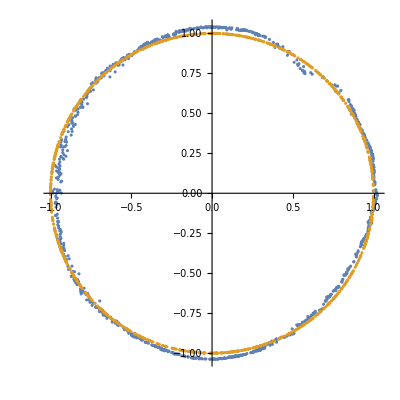

```mathematica
ListPlot[{vout,vin},AspectRatio->1]
```

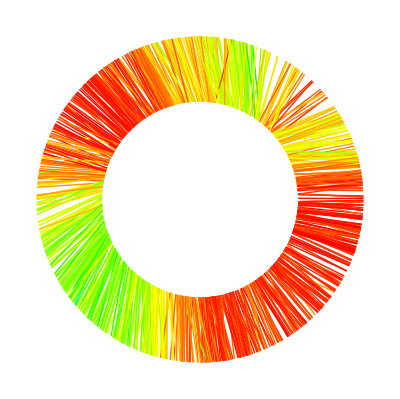

```mathematica
doubSig=Table[
vold= vin[[k]];
vnew=vout[[k]]/Norm[vout[[k]]];
{Hue[ArcCos[vold.vnew]],Line[{0.75 vold,1.25vnew}]},{k,1,Length[vout]}];

Graphics[{Red,doubSig}]
```

Data Sources Links/References

```mathematica
Hyperlink["Ironman helmet .stl file from thingiverse.com","https://www.thingiverse.com/thing:360747"]
```

Future Directions

It should be straightforward (but time consuming) to extend this approach to include all rotations, not only those about the vertical axis.  The parameter space is the full rotation group SO(3), which is a 3-dimensional manifold naturally embedded in 9-dimensional Euclidean space.    This will require training a network to output 9 parameters, the 9 components of the rotation matrix, while enforcing the constraints to constrain the resulting 9 numbers to be components of a rotation matrix.   I had  started the data generation as illustrated below, but had not worked on modifying the network appropriately.  There seem to still be some things to learn from fine-tuning the simpler case of rotations about the vertical axis, it seemed better to focus on that than to start this more ambitious generalization prematurely.

#### Routines for generating training/validation/data sets for full 3D rotation group. Data augmentation can be performed similarly.

output random SO3 matrix (not leaving any particular axis invariant)

```mathematica
randomSO3:=Module[{O3mat=RandomVariate[CircularRealMatrixDistribution[3]]},Det[O3mat] O3mat]
```

Generate lists

```mathematica
ClearAll[rasterSO3RotImage]
rasterSO3RotImage[randomSO3_]:=Module[{tempY,viewVec=randomSO3.{0,-1,0}}, 
(*ClearAll[tempY]; *)
tempY=Rasterize[Show[helmetType,ViewPoint->viewVec,Lighting->{
{"Directional",Hue[RandomReal[1]],{frontVec[viewVec],{0,0,0}}},{"Directional",Hue[RandomReal[1]],{frontVec[viewVec],{0,0,0}}},{"Directional",Hue[RandomReal[1]],{frontVec[viewVec],{0,0,0}}}
},ImageSize->imsize],"Image",ImageSize-> {imsize,imsize}]
]
```

```mathematica
ClearAll[nineComponent]
nineComponent[randomSO3_] :=Transpose[randomSO3]
```

```mathematica
tempRot=randomSO3;
rasterSO3RotImage[tempRot]-> nineComponent[tempRot]
```

-Graphics-→{{-0.970216,-0.103163,0.219178},{0.225635,-0.0556133,0.972623},{-0.0881496,0.993109,0.0772341}}

#### Initialization

Background Info Links/References

```mathematica
Hyperlink["Best Practices for Fine-tuning Visual Classifiers to New Domains, Brian Chu⋆, Vashisht Madhavan⋆, Oscar Beijbom, Judy Hoffman, Trevor Darrell","http://adas.cvc.uab.es/task-cv2016/papers/0002.pdf"]
```

```mathematica
Hyperlink["Deep Learning Part 2: Transfer Learning and Fine-tuning Deep Convolutional Neural Networks, Anusua Trivedi","http://blog.revolutionanalytics.com/2016/08/deep-learning-part-2.html"]
```

```mathematica
Hyperlink["Computer Vision Lab Dresden","http://cvlab-dresden.de/research/scene-understanding/pose-estimation/#DSAC"]
```

Keywords

Provide keywords as items

< Neural Networks >

< Rotations >

Other

Date

Last Modified: Tuesday, July 04, 2017

```mathematica
"Add Timestamp"
```